# Week-5:

```mathematica
f[x_]:=(2x+3)/(3x-1)
```

```mathematica
f[3]
```

9/8

```mathematica
N[%]
```

1.125

```mathematica
Simplify[x^2+2x+1]
```

(1+x)^2

```mathematica
FullSimplify[Integrate[1/(x^4-1),{x,-Pi/4,Pi/4}]]//N
```

-1.72508

```mathematica
NSolve[x^5-4x+5==0,x]
```

{{x→-1.63044},{x→-0.237094-1.51552 ⅈ},{x→-0.237094+1.51552 ⅈ},{x→1.05231-0.442637 ⅈ},{x→1.05231+0.442637 ⅈ}}

```mathematica
NSolve[{x^2+y^3==1,2x+3y==6},{x,y}]
```

{{x→9.88548,y→-4.59032},{x→1.24476-0.916754 ⅈ,y→1.17016+0.611169 ⅈ},{x→1.24476+0.916754 ⅈ,y→1.17016-0.611169 ⅈ}}

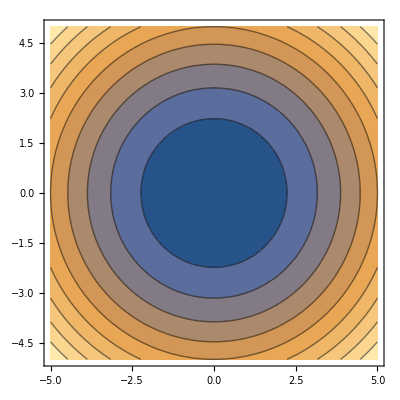

```mathematica
ContourPlot[x^2+y^2,{x,-5,5},{y,-5,5}]
```

```mathematica
ContourPlot3D[x^2+y^2+z^2,{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

```mathematica
Integrate[(1-Cos[2x])/(1+Cos[2x]),{x,0,1}]
```

-1+Tan[1]

```mathematica
a=Table[Prime[i],{i,10}]
```

{2,3,5,7,11,13,17,19,23,29}

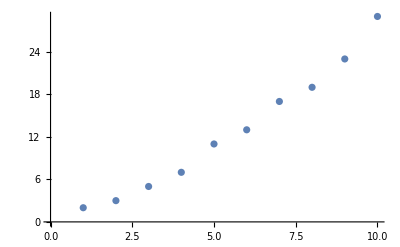

```mathematica
ListPlot[a]
```

```mathematica
ListPlot3D[{{2,3,5,7},{2,2,2,2},{11,13,17,19}},Mesh->All, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
p=ListPlot3D[{{2,3,5,7},{2,2,2,2},{11,13,17,19},{3,5,7,9}},Mesh->All, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{Sin[t]},{t,0,2Pi}]
```

```mathematica
q=RevolutionPlot3D[{Sin[t],Cos[2t]},{t,0,2Pi}]
```

-Graphics3D-

```mathematica
Show[p,q]
```

-Graphics3D-